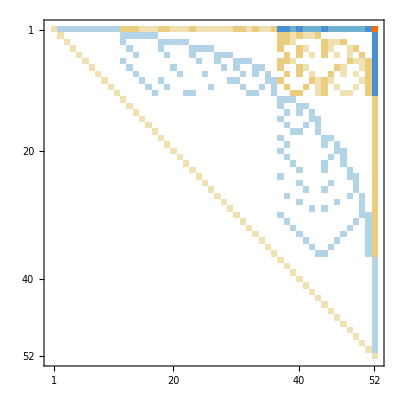

```mathematica
MatrixPlot[ConversionMatrix["C","E"]]
```

```mathematica
mat = Transpose[ConversionMatrix["C","E"]];
```

```mathematica
allGraphs5[K5Key,"colofourrealnull"]
```

24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5

```mathematica
allGraphs5[K5Key,"colofour"]
```

v1x2x3x4x5

```mathematica
vars=Map[ChangeSymbol[#,"c"]&,Bases["C","Variables"]]
```

{c1x2x3x4x5,c12x3x4x5,c13x2x4x5,c14x2x3x5,c15x2x3x4,c1x23x4x5,c1x24x3x5,c1x25x3x4,c1x2x34x5,c1x2x35x4,c1x2x3x45,c123x4x5,c124x3x5,c125x3x4,c12x34x5,c12x35x4,c12x3x45,c134x2x5,c135x2x4,c13x24x5,c13x25x4,c13x2x45,c145x2x3,c14x23x5,c14x25x3,c14x2x35,c15x23x4,c15x24x3,c15x2x34,c1x234x5,c1x235x4,c1x23x45,c1x245x3,c1x24x35,c1x25x34,c1x2x345,c1234x5,c1235x4,c123x45,c1245x3,c124x35,c125x34,c12x345,c1345x2,c134x25,c135x24,c13x245,c145x23,c14x235,c15x234,c1x2345,c12345}

```mathematica
repEtoM=Solve[Table[vars[[i]]==Total[Bases["E","Variables"].Map[Take[#,i]&,mat]],{i,52}],Bases["E","Variables"]]//First
```

{n1x2x3x4x5→c12345,n12x3x4x5→c12345+c12x345+c12x3x45+c12x3x4x5-c1x2345-c1x2x345-c1x2x3x45-c1x2x3x4x5,n13x2x4x5→c12345+c123x45+c123x4x5-c12x345-c12x3x45-c12x3x4x5+c13x245+c13x2x45+c13x2x4x5-c1x2345-c1x2x345-c1x2x3x45,n14x2x3x5→c12345+c1234x5-c123x45-c123x4x5+c124x35+c124x3x5-c12x345-c12x3x45+c134x25+c134x2x5-c13x245-c13x2x45-c13x2x4x5+c14x235+c14x2x35+c14x2x3x5-c1x2345-c1x2x345,n15x2x3x4→c12345-c1234x5+c1235x4-c123x45+c1245x3-c124x35-c124x3x5+c125x34+c125x3x4-c12x345+c1345x2-c134x25-c134x2x5+c135x24+c135x2x4-c13x245-c13x2x45+c145x23+c145x2x3-c14x235-c14x2x35-c14x2x3x5+c15x234+c15x2x34+c15x2x3x4-c1x2345,n1x23x4x5→c12345+c123x45+c123x4x5-c13x245-c145x2x3+c14x23x5-c14x2x35+c15x23x4-c15x2x34-c15x2x3x4+c1x23x45+c1x23x4x5-c1x2x345-c1x2x3x45,n1x24x3x5→c12345+c1234x5-c123x45-c123x4x5+c124x35+c124x3x5-c134x25-c135x2x4+c13x245+c13x24x5-c14x235-c15x23x4+c15x24x3-c15x2x34+c1x234x5-c1x23x45-c1x23x4x5+c1x24x35+c1x24x3x5-c1x2x345,n1x25x3x4→c12345-c1234x5+c1235x4-c123x45+c1245x3-c124x35-c124x3x5+c125x34+c125x3x4-c1345x2+c134x25-c135x24+c13x245-c13x24x5+c13x25x4-c145x23+c14x235-c14x23x5+c14x25x3-c15x234-c1x234x5+c1x235x4-c1x23x45+c1x245x3-c1x24x35-c1x24x3x5+c1x25x34+c1x25x3x4,n1x2x34x5→c12345+c1234x5-c124x35-c125x3x4+c12x34x5-c12x3x45+c134x25+c134x2x5-c14x235-c15x24x3+c1x234x5-c1x24x35-c1x25x3x4+c1x2x34x5,n1x2x35x4→c12345-c1234x5+c1235x4-c1245x3+c124x35-c125x34-c12x34x5+c12x35x4+c1345x2-c134x25-c134x2x5+c135x24+c135x2x4-c145x23+c14x235-c14x25x3+c14x2x35-c15x234-c1x234x5+c1x235x4-c1x245x3+c1x24x35-c1x25x34+c1x2x345-c1x2x34x5+c1x2x35x4,n1x2x3x45→c12345-c1235x4+c1245x3-c125x34-c12x35x4+c12x3x45+c1345x2-c135x24-c13x25x4+c145x23+c145x2x3-c15x234-c1x235x4+c1x245x3-c1x25x34+c1x2x345-c1x2x35x4+c1x2x3x45,n123x4x5→c12345+c123x45+c123x4x5-c1x2345-c1x2x345-c1x2x3x45,n124x3x5→c12345+c1234x5-c123x45-c123x4x5+c124x35+c124x3x5-c1x2345-c1x2x345,n125x3x4→c12345-c1234x5+c1235x4-c123x45+c1245x3-c124x35-c124x3x5+c125x34+c125x3x4-c1x2345,n12x34x5→c12345+c1234x5-c124x35-c125x3x4+c12x345+c12x34x5-c1x2345-c1x2x345,n12x35x4→c12345-c1234x5+c1235x4-c1245x3+c124x35-c125x34+c12x345-c12x34x5+c12x35x4-c1x2345,n12x3x45→c12345-c1235x4+c1245x3-c125x34+c12x345-c12x35x4+c12x3x45-c1x2345,n134x2x5→c12345+c1234x5-c12x345-c12x3x45+c134x25+c134x2x5-c1x2345-c1x2x345,n135x2x4→c12345-c1234x5+c1235x4-c12x345+c1345x2-c134x25-c134x2x5+c135x24+c135x2x4-c1x2345,n13x24x5→c12345+c1234x5-c134x25-c135x2x4+c13x245+c13x24x5-c1x2345-c1x2x345,n13x25x4→c12345-c1234x5+c1235x4-c1345x2+c134x25-c135x24+c13x245-c13x24x5+c13x25x4-c1x2345,n13x2x45→c12345-c1235x4+c123x45-c12x345+c1345x2-c135x24+c13x245-c13x25x4+c13x2x45-c1x2345,n145x2x3→c12345-c123x45+c1245x3-c12x345+c1345x2-c13x245-c13x2x45+c145x23+c145x2x3-c1x2345,n14x23x5→c12345+c1234x5-c13x245-c145x2x3+c14x235+c14x23x5-c1x2345-c1x2x345,n14x25x3→c12345-c123x45+c1245x3-c1345x2+c134x25-c145x23+c14x235-c14x23x5+c14x25x3-c1x2345,n14x2x35→c12345-c1245x3+c124x35-c12x345+c1345x2-c145x23+c14x235-c14x25x3+c14x2x35-c1x2345,n15x23x4→c12345-c1234x5+c1235x4-c13x245+c145x23-c14x235-c14x2x35+c15x234+c15x23x4-c1x2345,n15x24x3→c12345-c123x45+c1245x3-c134x25+c135x24-c14x235+c15x234-c15x23x4+c15x24x3-c1x2345,n15x2x34→c12345-c124x35+c125x34-c12x345+c1345x2-c14x235+c15x234-c15x24x3+c15x2x34-c1x2345,n1x234x5→c12345+c1234x5-c14x235-c15x2x34+c1x234x5-c1x2x345,n1x235x4→c12345-c1234x5+c1235x4-c145x23+c14x235-c15x234-c1x234x5+c1x235x4,n1x23x45→c12345-c1235x4+c123x45-c13x245+c145x23-c15x234-c1x235x4+c1x23x45,n1x245x3→c12345-c123x45+c1245x3-c135x24+c13x245-c15x234-c1x23x45+c1x245x3,n1x24x35→c12345-c1245x3+c124x35-c134x25+c135x24-c15x234-c1x245x3+c1x24x35,n1x25x34→c12345-c124x35+c125x34-c1345x2+c134x25-c15x234-c1x24x35+c1x25x34,n1x2x345→c12345-c125x34+c1345x2-c15x234-c1x25x34+c1x2x345,n1234x5→c12345+c1234x5-c1x2345-c1x2x345,n1235x4→c12345-c1234x5+c1235x4-c1x2345,n123x45→c12345-c1235x4+c123x45-c1x2345,n1245x3→c12345-c123x45+c1245x3-c1x2345,n124x35→c12345-c1245x3+c124x35-c1x2345,n125x34→c12345-c124x35+c125x34-c1x2345,n12x345→c12345-c125x34+c12x345-c1x2345,n1345x2→c12345-c12x345+c1345x2-c1x2345,n134x25→c12345-c1345x2+c134x25-c1x2345,n135x24→c12345-c134x25+c135x24-c1x2345,n13x245→c12345-c135x24+c13x245-c1x2345,n145x23→c12345-c13x245+c145x23-c1x2345,n14x235→c12345-c145x23+c14x235-c1x2345,n15x234→c12345-c14x235+c15x234-c1x2345,n1x2345→c12345-c15x234,n12345→c12345-c1x2345}

```mathematica
Table[allGraphs5[k,"colofourboega"]=Simplify[allGraphs5[k,"colofourrealnull"]/.repEtoM],{k,Keys[allGraphs5]}]
```

{c12345,-c12x345-c12x3x45-c12x3x4x5+c1x2345+c1x2x345+c1x2x3x45+c1x2x3x4x5,-c13x245-c13x2x45-c13x2x4x5+c1x2345+c1x2x345+c1x2x3x45+c1x2x3x4x5,1890,c1235x4-c1245x3+c125x34+c12x35x4-c12x3x45-c1345x2+c135x24+c13x25x4-c145x23-c145x2x3+c15x234+c1x235x4-c1x245x3+c1x25x34-c1x2x345+c1x2x35x4-c1x2x3x45,c12345-c1235x4+c1245x3-c125x34-c12x35x4+c12x3x45+c1345x2-c135x24-c13x25x4+c145x23+c145x2x3-c15x234-c1x235x4+c1x245x3-c1x25x34+c1x2x345-c1x2x35x4+c1x2x3x45}
 |  |  |  |

```mathematica
Table[ShowGraph5Least[k],{k,Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourboega"]]]==1&]}]
```

{-Graphics-034,-Graphics-295240,-Graphics-98410,-Graphics-32800,-Graphics-10930,-Graphics-3640}

```mathematica
Table[Table[Coefficient[Last[#],v],{v,vars}],{k,allGraphs5NullAtomKeys}]
```

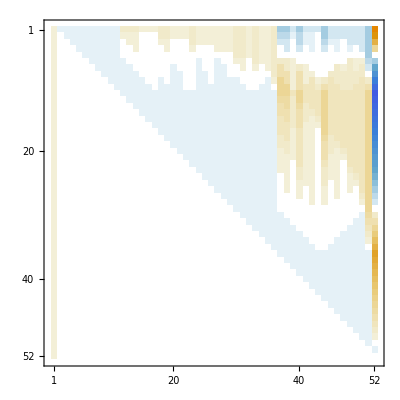

```mathematica
Map[Table[Coefficient[Last[#],v],{v,vars}]&,Solve[Table[vars[[i]]==Total[Bases["E","Variables"].Map[Take[#,i]&,mat]],{i,52}],Bases["E","Variables"]]//First]//Inverse//MatrixPlot
```

```mathematica
Bases["C","Variables"].Transpose[mat]//MatrixForm
```

(v1x2x3x4x5
v12x3x4x5-v1x2x3x4x5
v13x2x4x5-v1x2x3x4x5
v14x2x3x5-v1x2x3x4x5
v15x2x3x4-v1x2x3x4x5
v1x23x4x5-v1x2x3x4x5
v1x24x3x5-v1x2x3x4x5
v1x25x3x4-v1x2x3x4x5
v1x2x34x5-v1x2x3x4x5
v1x2x35x4-v1x2x3x4x5
v1x2x3x45-v1x2x3x4x5
v123x4x5-v12x3x4x5-v13x2x4x5-v1x23x4x5+2 v1x2x3x4x5
v124x3x5-v12x3x4x5-v14x2x3x5-v1x24x3x5+2 v1x2x3x4x5
v125x3x4-v12x3x4x5-v15x2x3x4-v1x25x3x4+2 v1x2x3x4x5
v12x34x5-v12x3x4x5-v1x2x34x5+v1x2x3x4x5
v12x35x4-v12x3x4x5-v1x2x35x4+v1x2x3x4x5
v12x3x45-v12x3x4x5-v1x2x3x45+v1x2x3x4x5
v134x2x5-v13x2x4x5-v14x2x3x5-v1x2x34x5+2 v1x2x3x4x5
v135x2x4-v13x2x4x5-v15x2x3x4-v1x2x35x4+2 v1x2x3x4x5
v13x24x5-v13x2x4x5-v1x24x3x5+v1x2x3x4x5
v13x25x4-v13x2x4x5-v1x25x3x4+v1x2x3x4x5
v13x2x45-v13x2x4x5-v1x2x3x45+v1x2x3x4x5
v145x2x3-v14x2x3x5-v15x2x3x4-v1x2x3x45+2 v1x2x3x4x5
v14x23x5-v14x2x3x5-v1x23x4x5+v1x2x3x4x5
v14x25x3-v14x2x3x5-v1x25x3x4+v1x2x3x4x5
v14x2x35-v14x2x3x5-v1x2x35x4+v1x2x3x4x5
v15x23x4-v15x2x3x4-v1x23x4x5+v1x2x3x4x5
v15x24x3-v15x2x3x4-v1x24x3x5+v1x2x3x4x5
v15x2x34-v15x2x3x4-v1x2x34x5+v1x2x3x4x5
v1x234x5-v1x23x4x5-v1x24x3x5-v1x2x34x5+2 v1x2x3x4x5
v1x235x4-v1x23x4x5-v1x25x3x4-v1x2x35x4+2 v1x2x3x4x5
v1x23x45-v1x23x4x5-v1x2x3x45+v1x2x3x4x5
v1x245x3-v1x24x3x5-v1x25x3x4-v1x2x3x45+2 v1x2x3x4x5
v1x24x35-v1x24x3x5-v1x2x35x4+v1x2x3x4x5
v1x25x34-v1x25x3x4-v1x2x34x5+v1x2x3x4x5
v1x2x345-v1x2x34x5-v1x2x35x4-v1x2x3x45+2 v1x2x3x4x5
v1234x5-v123x4x5-v124x3x5-v12x34x5+2 v12x3x4x5-v134x2x5-v13x24x5+2 v13x2x4x5-v14x23x5+2 v14x2x3x5-v1x234x5+2 v1x23x4x5+2 v1x24x3x5+2 v1x2x34x5-6 v1x2x3x4x5
v1235x4-v123x4x5-v125x3x4-v12x35x4+2 v12x3x4x5-v135x2x4-v13x25x4+2 v13x2x4x5-v15x23x4+2 v15x2x3x4-v1x235x4+2 v1x23x4x5+2 v1x25x3x4+2 v1x2x35x4-6 v1x2x3x4x5
v123x45-v123x4x5-v12x3x45+v12x3x4x5-v13x2x45+v13x2x4x5-v1x23x45+v1x23x4x5+2 v1x2x3x45-2 v1x2x3x4x5
v1245x3-v124x3x5-v125x3x4-v12x3x45+2 v12x3x4x5-v145x2x3-v14x25x3+2 v14x2x3x5-v15x24x3+2 v15x2x3x4-v1x245x3+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x3x45-6 v1x2x3x4x5
v124x35-v124x3x5-v12x35x4+v12x3x4x5-v14x2x35+v14x2x3x5-v1x24x35+v1x24x3x5+2 v1x2x35x4-2 v1x2x3x4x5
v125x34-v125x3x4-v12x34x5+v12x3x4x5-v15x2x34+v15x2x3x4-v1x25x34+v1x25x3x4+2 v1x2x34x5-2 v1x2x3x4x5
v12x345-v12x34x5-v12x35x4-v12x3x45+2 v12x3x4x5-v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45-2 v1x2x3x4x5
v1345x2-v134x2x5-v135x2x4-v13x2x45+2 v13x2x4x5-v145x2x3-v14x2x35+2 v14x2x3x5-v15x2x34+2 v15x2x3x4-v1x2x345+2 v1x2x34x5+2 v1x2x35x4+2 v1x2x3x45-6 v1x2x3x4x5
v134x25-v134x2x5-v13x25x4+v13x2x4x5-v14x25x3+v14x2x3x5-v1x25x34+2 v1x25x3x4+v1x2x34x5-2 v1x2x3x4x5
v135x24-v135x2x4-v13x24x5+v13x2x4x5-v15x24x3+v15x2x3x4-v1x24x35+2 v1x24x3x5+v1x2x35x4-2 v1x2x3x4x5
v13x245-v13x24x5-v13x25x4-v13x2x45+2 v13x2x4x5-v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45-2 v1x2x3x4x5
v145x23-v145x2x3-v14x23x5+v14x2x3x5-v15x23x4+v15x2x3x4-v1x23x45+2 v1x23x4x5+v1x2x3x45-2 v1x2x3x4x5
v14x235-v14x23x5-v14x25x3-v14x2x35+2 v14x2x3x5-v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4-2 v1x2x3x4x5
v15x234-v15x23x4-v15x24x3-v15x2x34+2 v15x2x3x4-v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5-2 v1x2x3x4x5
v1x2345-v1x234x5-v1x235x4-v1x23x45+2 v1x23x4x5-v1x245x3-v1x24x35+2 v1x24x3x5-v1x25x34+2 v1x25x3x4-v1x2x345+2 v1x2x34x5+2 v1x2x35x4+2 v1x2x3x45-6 v1x2x3x4x5
v12345-v1234x5-v1235x4-v123x45+2 v123x4x5-v1245x3-v124x35+2 v124x3x5-v125x34+2 v125x3x4-v12x345+2 v12x34x5+2 v12x35x4+2 v12x3x45-6 v12x3x4x5-v1345x2-v134x25+2 v134x2x5-v135x24+2 v135x2x4-v13x245+2 v13x24x5+2 v13x25x4+2 v13x2x45-6 v13x2x4x5-v145x23+2 v145x2x3-v14x235+2 v14x23x5+2 v14x25x3+2 v14x2x35-6 v14x2x3x5-v15x234+2 v15x23x4+2 v15x24x3+2 v15x2x34-6 v15x2x3x4-v1x2345+2 v1x234x5+2 v1x235x4+2 v1x23x45-6 v1x23x4x5+2 v1x245x3+2 v1x24x35-6 v1x24x3x5+2 v1x25x34-6 v1x25x3x4+2 v1x2x345-6 v1x2x34x5-6 v1x2x35x4-6 v1x2x3x45+24 v1x2x3x4x5)

```mathematica
Bases["C","Variables"].mat//MatrixForm
```

(24 v12345-6 v1234x5-6 v1235x4-2 v123x45+2 v123x4x5-6 v1245x3-2 v124x35+2 v124x3x5-2 v125x34+2 v125x3x4-2 v12x345+v12x34x5+v12x35x4+v12x3x45-v12x3x4x5-6 v1345x2-2 v134x25+2 v134x2x5-2 v135x24+2 v135x2x4-2 v13x245+v13x24x5+v13x25x4+v13x2x45-v13x2x4x5-2 v145x23+2 v145x2x3-2 v14x235+v14x23x5+v14x25x3+v14x2x35-v14x2x3x5-2 v15x234+v15x23x4+v15x24x3+v15x2x34-v15x2x3x4-6 v1x2345+2 v1x234x5+2 v1x235x4+v1x23x45-v1x23x4x5+2 v1x245x3+v1x24x35-v1x24x3x5+v1x25x34-v1x25x3x4+2 v1x2x345-v1x2x34x5-v1x2x35x4-v1x2x3x45+v1x2x3x4x5
-6 v12345+2 v1234x5+2 v1235x4+v123x45-v123x4x5+2 v1245x3+v124x35-v124x3x5+v125x34-v125x3x4+2 v12x345-v12x34x5-v12x35x4-v12x3x45+v12x3x4x5
-6 v12345+2 v1234x5+2 v1235x4+v123x45-v123x4x5+2 v1345x2+v134x25-v134x2x5+v135x24-v135x2x4+2 v13x245-v13x24x5-v13x25x4-v13x2x45+v13x2x4x5
-6 v12345+2 v1234x5+2 v1245x3+v124x35-v124x3x5+2 v1345x2+v134x25-v134x2x5+v145x23-v145x2x3+2 v14x235-v14x23x5-v14x25x3-v14x2x35+v14x2x3x5
-6 v12345+2 v1235x4+2 v1245x3+v125x34-v125x3x4+2 v1345x2+v135x24-v135x2x4+v145x23-v145x2x3+2 v15x234-v15x23x4-v15x24x3-v15x2x34+v15x2x3x4
-6 v12345+2 v1234x5+2 v1235x4+v123x45-v123x4x5+2 v145x23+v14x235-v14x23x5+v15x234-v15x23x4+2 v1x2345-v1x234x5-v1x235x4-v1x23x45+v1x23x4x5
-6 v12345+2 v1234x5+2 v1245x3+v124x35-v124x3x5+2 v135x24+v13x245-v13x24x5+v15x234-v15x24x3+2 v1x2345-v1x234x5-v1x245x3-v1x24x35+v1x24x3x5
-6 v12345+2 v1235x4+2 v1245x3+v125x34-v125x3x4+2 v134x25+v13x245-v13x25x4+v14x235-v14x25x3+2 v1x2345-v1x235x4-v1x245x3-v1x25x34+v1x25x3x4
-6 v12345+2 v1234x5+2 v125x34+v12x345-v12x34x5+2 v1345x2+v134x25-v134x2x5+v15x234-v15x2x34+2 v1x2345-v1x234x5-v1x25x34-v1x2x345+v1x2x34x5
-6 v12345+2 v1235x4+2 v124x35+v12x345-v12x35x4+2 v1345x2+v135x24-v135x2x4+v14x235-v14x2x35+2 v1x2345-v1x235x4-v1x24x35-v1x2x345+v1x2x35x4
-6 v12345+2 v123x45+2 v1245x3+v12x345-v12x3x45+2 v1345x2+v13x245-v13x2x45+v145x23-v145x2x3+2 v1x2345-v1x23x45-v1x245x3-v1x2x345+v1x2x3x45
2 v12345-v1234x5-v1235x4-v123x45+v123x4x5
2 v12345-v1234x5-v1245x3-v124x35+v124x3x5
2 v12345-v1235x4-v1245x3-v125x34+v125x3x4
2 v12345-v1234x5-v125x34-v12x345+v12x34x5
2 v12345-v1235x4-v124x35-v12x345+v12x35x4
2 v12345-v123x45-v1245x3-v12x345+v12x3x45
2 v12345-v1234x5-v1345x2-v134x25+v134x2x5
2 v12345-v1235x4-v1345x2-v135x24+v135x2x4
2 v12345-v1234x5-v135x24-v13x245+v13x24x5
2 v12345-v1235x4-v134x25-v13x245+v13x25x4
2 v12345-v123x45-v1345x2-v13x245+v13x2x45
2 v12345-v1245x3-v1345x2-v145x23+v145x2x3
2 v12345-v1234x5-v145x23-v14x235+v14x23x5
2 v12345-v1245x3-v134x25-v14x235+v14x25x3
2 v12345-v124x35-v1345x2-v14x235+v14x2x35
2 v12345-v1235x4-v145x23-v15x234+v15x23x4
2 v12345-v1245x3-v135x24-v15x234+v15x24x3
2 v12345-v125x34-v1345x2-v15x234+v15x2x34
2 v12345-v1234x5-v15x234-v1x2345+v1x234x5
2 v12345-v1235x4-v14x235-v1x2345+v1x235x4
2 v12345-v123x45-v145x23-v1x2345+v1x23x45
2 v12345-v1245x3-v13x245-v1x2345+v1x245x3
2 v12345-v124x35-v135x24-v1x2345+v1x24x35
2 v12345-v125x34-v134x25-v1x2345+v1x25x34
2 v12345-v12x345-v1345x2-v1x2345+v1x2x345
-v12345+v1234x5
-v12345+v1235x4
-v12345+v123x45
-v12345+v1245x3
-v12345+v124x35
-v12345+v125x34
-v12345+v12x345
-v12345+v1345x2
-v12345+v134x25
-v12345+v135x24
-v12345+v13x245
-v12345+v145x23
-v12345+v14x235
-v12345+v15x234
-v12345+v1x2345
v12345)

```mathematica
repCtoM=Solve[Table[vars[[i]]==Total[Bases["C","Variables"].Map[Take[#,i]&,mat]],{i,52}],Bases["C","Variables"]]//First
```

{v1x2x3x4x5→c12345,v12x3x4x5→c12345+c12x345+c12x3x45+c12x3x4x5-c1x2345-c1x2x345-c1x2x3x45-c1x2x3x4x5,v13x2x4x5→c12345+c123x45+c123x4x5-c12x345-c12x3x45-c12x3x4x5+c13x245+c13x2x45+c13x2x4x5-c1x2345-c1x2x345-c1x2x3x45,v14x2x3x5→c12345+c1234x5-c123x45-c123x4x5+c124x35+c124x3x5-c12x345-c12x3x45+c134x25+c134x2x5-c13x245-c13x2x45-c13x2x4x5+c14x235+c14x2x35+c14x2x3x5-c1x2345-c1x2x345,v15x2x3x4→c12345-c1234x5+c1235x4-c123x45+c1245x3-c124x35-c124x3x5+c125x34+c125x3x4-c12x345+c1345x2-c134x25-c134x2x5+c135x24+c135x2x4-c13x245-c13x2x45+c145x23+c145x2x3-c14x235-c14x2x35-c14x2x3x5+c15x234+c15x2x34+c15x2x3x4-c1x2345,v1x23x4x5→c12345+c123x45+c123x4x5-c13x245-c145x2x3+c14x23x5-c14x2x35+c15x23x4-c15x2x34-c15x2x3x4+c1x23x45+c1x23x4x5-c1x2x345-c1x2x3x45,v1x24x3x5→c12345+c1234x5-c123x45-c123x4x5+c124x35+c124x3x5-c134x25-c135x2x4+c13x245+c13x24x5-c14x235-c15x23x4+c15x24x3-c15x2x34+c1x234x5-c1x23x45-c1x23x4x5+c1x24x35+c1x24x3x5-c1x2x345,v1x25x3x4→c12345-c1234x5+c1235x4-c123x45+c1245x3-c124x35-c124x3x5+c125x34+c125x3x4-c1345x2+c134x25-c135x24+c13x245-c13x24x5+c13x25x4-c145x23+c14x235-c14x23x5+c14x25x3-c15x234-c1x234x5+c1x235x4-c1x23x45+c1x245x3-c1x24x35-c1x24x3x5+c1x25x34+c1x25x3x4,v1x2x34x5→c12345+c1234x5-c124x35-c125x3x4+c12x34x5-c12x3x45+c134x25+c134x2x5-c14x235-c15x24x3+c1x234x5-c1x24x35-c1x25x3x4+c1x2x34x5,v1x2x35x4→c12345-c1234x5+c1235x4-c1245x3+c124x35-c125x34-c12x34x5+c12x35x4+c1345x2-c134x25-c134x2x5+c135x24+c135x2x4-c145x23+c14x235-c14x25x3+c14x2x35-c15x234-c1x234x5+c1x235x4-c1x245x3+c1x24x35-c1x25x34+c1x2x345-c1x2x34x5+c1x2x35x4,v1x2x3x45→c12345-c1235x4+c1245x3-c125x34-c12x35x4+c12x3x45+c1345x2-c135x24-c13x25x4+c145x23+c145x2x3-c15x234-c1x235x4+c1x245x3-c1x25x34+c1x2x345-c1x2x35x4+c1x2x3x45,v123x4x5→c12345+c123x45+c123x4x5-c1x2345-c1x2x345-c1x2x3x45,v124x3x5→c12345+c1234x5-c123x45-c123x4x5+c124x35+c124x3x5-c1x2345-c1x2x345,v125x3x4→c12345-c1234x5+c1235x4-c123x45+c1245x3-c124x35-c124x3x5+c125x34+c125x3x4-c1x2345,v12x34x5→c12345+c1234x5-c124x35-c125x3x4+c12x345+c12x34x5-c1x2345-c1x2x345,v12x35x4→c12345-c1234x5+c1235x4-c1245x3+c124x35-c125x34+c12x345-c12x34x5+c12x35x4-c1x2345,v12x3x45→c12345-c1235x4+c1245x3-c125x34+c12x345-c12x35x4+c12x3x45-c1x2345,v134x2x5→c12345+c1234x5-c12x345-c12x3x45+c134x25+c134x2x5-c1x2345-c1x2x345,v135x2x4→c12345-c1234x5+c1235x4-c12x345+c1345x2-c134x25-c134x2x5+c135x24+c135x2x4-c1x2345,v13x24x5→c12345+c1234x5-c134x25-c135x2x4+c13x245+c13x24x5-c1x2345-c1x2x345,v13x25x4→c12345-c1234x5+c1235x4-c1345x2+c134x25-c135x24+c13x245-c13x24x5+c13x25x4-c1x2345,v13x2x45→c12345-c1235x4+c123x45-c12x345+c1345x2-c135x24+c13x245-c13x25x4+c13x2x45-c1x2345,v145x2x3→c12345-c123x45+c1245x3-c12x345+c1345x2-c13x245-c13x2x45+c145x23+c145x2x3-c1x2345,v14x23x5→c12345+c1234x5-c13x245-c145x2x3+c14x235+c14x23x5-c1x2345-c1x2x345,v14x25x3→c12345-c123x45+c1245x3-c1345x2+c134x25-c145x23+c14x235-c14x23x5+c14x25x3-c1x2345,v14x2x35→c12345-c1245x3+c124x35-c12x345+c1345x2-c145x23+c14x235-c14x25x3+c14x2x35-c1x2345,v15x23x4→c12345-c1234x5+c1235x4-c13x245+c145x23-c14x235-c14x2x35+c15x234+c15x23x4-c1x2345,v15x24x3→c12345-c123x45+c1245x3-c134x25+c135x24-c14x235+c15x234-c15x23x4+c15x24x3-c1x2345,v15x2x34→c12345-c124x35+c125x34-c12x345+c1345x2-c14x235+c15x234-c15x24x3+c15x2x34-c1x2345,v1x234x5→c12345+c1234x5-c14x235-c15x2x34+c1x234x5-c1x2x345,v1x235x4→c12345-c1234x5+c1235x4-c145x23+c14x235-c15x234-c1x234x5+c1x235x4,v1x23x45→c12345-c1235x4+c123x45-c13x245+c145x23-c15x234-c1x235x4+c1x23x45,v1x245x3→c12345-c123x45+c1245x3-c135x24+c13x245-c15x234-c1x23x45+c1x245x3,v1x24x35→c12345-c1245x3+c124x35-c134x25+c135x24-c15x234-c1x245x3+c1x24x35,v1x25x34→c12345-c124x35+c125x34-c1345x2+c134x25-c15x234-c1x24x35+c1x25x34,v1x2x345→c12345-c125x34+c1345x2-c15x234-c1x25x34+c1x2x345,v1234x5→c12345+c1234x5-c1x2345-c1x2x345,v1235x4→c12345-c1234x5+c1235x4-c1x2345,v123x45→c12345-c1235x4+c123x45-c1x2345,v1245x3→c12345-c123x45+c1245x3-c1x2345,v124x35→c12345-c1245x3+c124x35-c1x2345,v125x34→c12345-c124x35+c125x34-c1x2345,v12x345→c12345-c125x34+c12x345-c1x2345,v1345x2→c12345-c12x345+c1345x2-c1x2345,v134x25→c12345-c1345x2+c134x25-c1x2345,v135x24→c12345-c134x25+c135x24-c1x2345,v13x245→c12345-c135x24+c13x245-c1x2345,v145x23→c12345-c13x245+c145x23-c1x2345,v14x235→c12345-c145x23+c14x235-c1x2345,v15x234→c12345-c14x235+c15x234-c1x2345,v1x2345→c12345-c15x234,v12345→c12345-c1x2345}

```mathematica
Table[allGraphs5[k,"colofourboega"]=Simplify[allGraphs5[k,"colofour"]/.repCtoM],{k,Keys[allGraphs5]}]
```

{52 c12345+5 c1235x4-5 c123x45+5 c1245x3+c125x3x4-5 c12x345-c12x3x45+5 c1345x2+c135x2x4-c13x2x45+c145x2x3-5 c15x234-c15x2x34-37 c1x2345+c1x235x4-c1x23x45+c1x245x3-c1x25x34-10 c1x2x345-3 c1x2x3x45-c1x2x3x4x5,1893,15 c12345-5 c1235x4+5 c1245x3-4 c125x34-c12x345-2 c12x35x4+2 c12x3x45+5 c1345x2-4 c135x24-2 c13x25x4+4 c145x23+2 c145x2x3-5 c15x234-10 c1x2345-2 c1x235x4+2 c1x245x3-2 c1x25x34+2 c1x2x345-c1x2x35x4+c1x2x3x45}
 |  |  |  |

```mathematica
Table[ShowGraph5Least[k],{k,Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourboega"]]]==3&]}]
```

{-Graphics-7282}

```mathematica
Sort[Tally[Table[Length[ListofVars[allGraphs5[k,"colofourboega"]]],{k,Keys[allGraphs5]}]]]
```

{{1,1},{2,2},{3,1},{4,28},{6,5},{7,10},{8,45},{9,54},{10,91},{11,1},{12,8},{13,8},{14,10},{15,27},{16,31},{17,24},{18,42},{19,42},{20,65},{21,62},{22,44},{23,70},{24,47},{25,32},{26,40},{27,55},{28,87},{29,86},{30,33},{31,45},{32,46},{33,34},{34,51},{35,72},{36,77},{37,85},{38,110},{39,107},{40,79},{41,67},{42,32},{43,23},{44,9},{45,5},{46,2}}

```mathematica
Sort[Tally[Table[Length[ListofVars[allGraphs5[k,"colofourboega"]]],{k,allGraphs5AtomKeys}]]]
```

{{1,1},{2,2},{4,14},{6,3},{8,12},{10,11},{12,1},{14,2},{18,2},{20,1},{26,2},{28,1}}

```mathematica
Sort[Tally[Table[Length[ListofVars[allGraphs5[k,"colofourboega"]]],{k,allGraphs5NullAtomKeys}]]]
```

{{2,1},{3,1},{4,14},{6,1},{7,2},{8,6},{9,5},{10,11},{12,1},{15,1},{18,1},{20,2},{21,2},{24,1},{26,1},{28,1},{29,1}}

```mathematica
Sort[Tally[Table[Length[ListofVars[allGraphs5[k,"colofourboega"]]],{k,allGraphs5GeneratorAtomKeys}]]]
```

{{1,1},{8,1},{12,1},{14,2},{15,1},{16,1},{17,1},{18,2},{19,2},{20,3},{21,2},{23,4},{25,4},{26,5},{27,1},{28,2},{29,2},{30,3},{31,3},{32,2},{34,1},{35,1},{36,4},{37,1},{38,1},{40,1}}

```mathematica
G
```

```mathematica
Table[Length[ListofVars[allGraphs5[k,"colofourgenerator"]]],{k,keys5}]
```

```mathematica
keys5=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&];Length[keys5]
```

1024

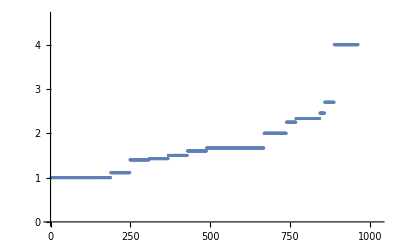

```mathematica
Table[Length[ListofVars[allGraphs5[k,"colofour"]]]/Length[ListofVars[allGraphs5[k,"colofourgenerator"]]],{k,keys5}]//Sort//ListPlot
```

```mathematica
keys6=Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&];Length[keys6]
```

32768

```mathematica
Table[Length[ListofVars[allGraphs6[k,"colofour"]]]/Length[ListofVars[allGraphs6[k,"colofourgenerator"]]],{k,keys6}]//Sort//ListPlot
```